```mathematica
(*Introduction part a*)
{FullForm[a*b+c], FullForm[a+b*c]} (*showing what operations have precedence*)
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)] (*Using parentheses to specify order of operations*)
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y≻y ∧ m ≠ 0 ⇒ n ⧐̸ m
```

∀_x∃_y x⊗y≻y&&m≠0⇒n⧐̸m

```mathematica
FullForm[%] (*FullForm shows the structure of the expression*)
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
(*There are flat, left grouping, and right grouping types of operators*)
(*Plus is a flat operator, no grouping is necessary*)
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d] (*not flat so it gets grouped in pairs*)
```

Power[a,Power[b,Power[c,d]]]

```mathematica
(*some special characters are operators as well*)
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a×a×a×b×b×c (*× means same as '*'*)
```

a^3 b^2 c

```mathematica
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x] b[x] ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
\!\(\*SubscriptBox[\(∂\),\(x\)]\*SuperscriptBox[\(x\),\(n\)]\)
```

n x^(-1+n)

```mathematica
∂_x x^n (*What I typed above is supposed to look like this*)
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s + n
```

n+Zeta[s]

```mathematica
(*Introduction part b*)
Factor[x^6-1]
```

(-1+x) (1+x) (1-x+x^2) (1+x+x^2)

```mathematica
FullForm[{a,b,c}] (*can label diff types of data to be used by later operands such as creating a list*)
```

List[a,b,c]

```mathematica
point[a,b,c] (*point does nothing but store these under the head point so they can be used later*)
```

point[a,b,c]

```mathematica
(*Introduction part c*)
(*4 differnt types of brackets:
parentheses for grouping, square brackets for functions, curly braces for lists, and double brackets for indexing*)
```

```mathematica
(*Introduction part d*)
1+2/3
```

5/3

```mathematica
(1+2)/3 (*effect of parentheses for grouping*)
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3x==12,Sqrt[9+y],"hello"} (*lists can contain anything*)
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,1,{3,4,5},{3,2}} (*lists can contain other lists*)
```

{1,1,{3,4,5},{3,2}}

```mathematica
(*Square brackets enclose the arguments of functions*)
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]] (*double square brackets used for indexing*)
```

9

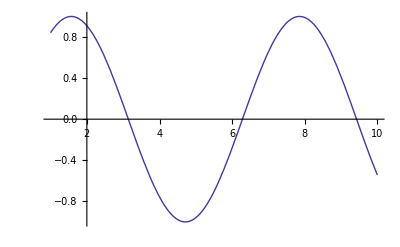

```mathematica
(*Plot a function,with the range of the plot specified in a list*)
Plot[Sin[x],{x,1,10}]
```

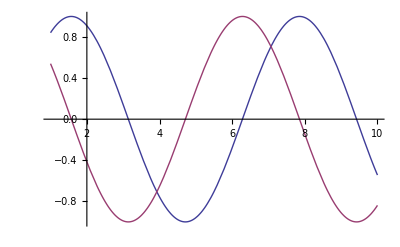

```mathematica
(*Plot two functions togetherthe pair of functions is in a list*)
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*Symbolic Analysis part a*)
```